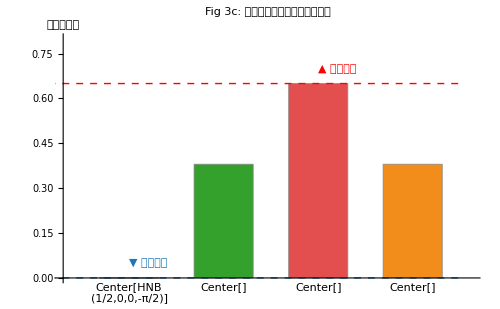

```mathematica
(* =========================================*)(*Fig 3c:不同半斯格明子的自由能比较*)ClearAll["Global`*"]

(*数据*)
energies={0.00,0.38,0.65,0.38};
barColors={RGBColor[0.12,0.47,0.71],RGBColor[0.20,0.63,0.17],RGBColor[0.89,0.31,0.31],RGBColor[0.95,0.55,0.10]};

BarChart[energies,ChartLabels->{Placed[Style["HAS\n(1/2,-1/2,0,0)",13,Bold,barColors[[1]]],Below,Center],Placed[Style["HNB\n(1/2,0,0,π/2)",13,Bold,barColors[[2]]],Below,Center],Placed[Style["HNS\n(1/2,1/2,0,π)",13,Bold,barColors[[3]]],Below,Center],Placed[Style["HNB\n(1/2,0,0,-π/2)",13,Bold,barColors[[4]]],Below,Center]},ChartStyle->barColors,ChartBaseStyle->EdgeForm[{Thin,Gray}],Axes->{False,True},AxesLabel->{"",Style["相对自由能",14]},PlotLabel->Style["Fig 3c: 不同半斯格明子的自由能比较",16,Bold],PlotRange->{0,0.8},ImageSize->500,BarSpacing->0.6,Epilog->{{Red,Dashed,Line[{{0,0.65},{4.5,0.65}}]},{Red,Text[Style["▲ 能量最高",11,Red],{3.2,0.70}]},{RGBColor[0.12,0.47,0.71],Dashed,Line[{{0,0},{4.5,0}}]},{RGBColor[0.12,0.47,0.71],Text[Style["▼ 能量最低",11,RGBColor[0.12,0.47,0.71]],{1.2,0.05}]}}]
```